## 138Nd

```mathematica
ClearAll["Global`*"]
```

```mathematica
L7En=Sort[{6241.2,5468.9,4974.1}];
L7Spins={13,15,17};
L6En=Sort[{5028.6,3821.7,3174.7}];
L6Spins={10,12,14};
L7En=L7En/1000;
L6En=L6En/1000;
```

```mathematica
plotfile1="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/138Nd.pdf";
```

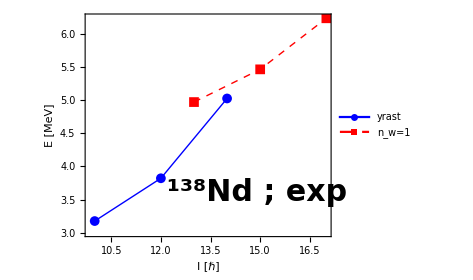

```mathematica
data1=Table[{L6Spins[[i]],L6En[[i]]},{i,1,Length[L6En]}];
data2=Table[{L7Spins[[i]],L7En[[i]]},{i,1,Length[L7En]}];
fig=ListPlot[{data1,data2},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{"yrast","n_w=1"},{0.25,0.8}],ImageSize->350,PlotRange->{Full,Full},Epilog->{ Inset[Style[Row[{Superscript["","138"],"Nd ; exp"}],Bold,30],Scaled[{0.7,0.2}]]}];
Export[plotfile1,fig];
Show[fig]
```